```mathematica
equations:={s'[t]==-β s[t] i[t],i'[t]==β s[t] i[t]-γ i[t],r'[t]==γ i[t]}
ic:={s[0]==99.,i[0]==1.,r[0]==0.}
parameters:={β->.005,γ->.2}
```

```mathematica
sol=NDSolve[{equations/.parameters,ic},{s,i,r},{t,0,50}]
```

{{s→InterpolatingFunction[…],i→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

```mathematica
Plot[
Evaluate[{s[t],i[t],r[t]}/. sol],
{t,0,50},
PlotLabels->{s[t],i[t],r[t]},
PlotRange->All
]
```

-Graphics-

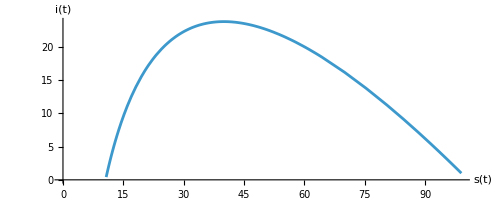

```mathematica
ParametricPlot[
Evaluate[{s[t],i[t]}/. sol],
{t,0,50},
AxesLabel->{s[t],i[t]}
]
```

```mathematica
Reduce[Last/@equations==0,{s[t],i[t],r[t]}]
```

(γ==0&&β==0)||(γ==0&&s[t]==0)||i[t]==0

```mathematica
D[Last/@equations,{{s[t],i[t],r[t]}}]/.{i[t]->0,r[t]->0,s[t]->1}
```

{{0,-β,0},{0,β-γ,0},{0,γ,0}}

```mathematica
Eigenvalues[%/.parameters]
```

{-0.195,0.,0.}

```mathematica
FindMaximum[Evaluate[i[t]/. sol],{t,0,50}]
```

{23.7504,{t→16.5091}}

```mathematica
Evaluate[r[50]/. sol]
```

{88.8458}

```mathematica
Manipulate[
sol=NDSolve[{equations/. {β->b,γ->0.1},ic},{s,i,r},{t,0,50}];
Plot[Evaluate[i[t]/. sol],{t,0,50},PlotRange->All],
{b,0.0005,0.005}
]
```